# Skeleton Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	(*If[Length[AdjacencyList[graph,i]]>2,AppendTo[ans,{i,Length[AdjacencyList[graph,i]]}]]];*)
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

mergeScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {{x1,y1,z1},r1} 
	ball2: {{x2,y2,z2},r2}

```mathematica
mergeScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦2⟧,ball2⟦2⟧];
	r2 = Min[ball1⟦2⟧,ball2⟦2⟧];
	d = EuclideanDistance[ball1⟦1⟧, ball2⟦1⟧];
	score = (r1 + r2 - d)/(2*r2);
	score
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Return[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = deleteNode[g, nodesDeg2⟦1⟧];
		nodesDeg2 = Drop[nodesDeg2,1];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, {x,y,z},r}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦3⟧;
	r1 = ball1⟦4⟧;
	c2 = ball2⟦3⟧;
	r2 = ball2⟦4⟧;
	d = EuclideanDistance[c1, c2];
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: list of all junctions: {identifier, degree, {x,y,z},r}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, {x,y,z},r}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3} = smallestCircumBall[ball1,ball2];
	
	newBall = {v1,newDegree,c3,r3};
	newJunctionList = DeleteCases[junctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];
	
	{newJunctionList, g}
]
```

```mathematica
computeCN:=Function[{junctionList,graph},
	J = junctionList;
	G = graph;
	threshold = 0;
	While[True,
		maxScore = threshold-1;
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			If[j1 == j2, Continue[]];
			
			ball1 = Select[J,#⟦1⟧ == j1 &];
			ball2 = Select[J,#⟦1⟧ == j2 &];
			score = mergeScore[ball1,ball2];
			If[score > maxScore,
				maxScore = score;
				tgt1 = ball1;
				tgt2 = ball2;
			]
		,{edge,edges}];
		
		If[maxScore < threshold,Break[]];
		{J,G} = mergeJunctions[J,G,tgt1,tgt2];
	];
	{J,G}
]
```

## Function Test

### test data

```mathematica
testG =
```

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

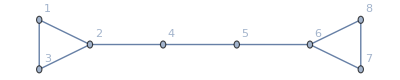

-Graphics3D-

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
s = simplifyGraph[g];
GraphPlot3D[s]
```

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

1/4 (8-3 √3)

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

{{0.0119,0.0594998,0.0713998},1.0937}

-Graphics3D-

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Import data from files

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
maRawData = Import["data\\scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;

maPoints = maTable⟦;;86117,;;⟧;
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
numOfPoints = 12326;
numOfEdges = 12468;

skelRawData = Import["data\\scoba12_small_skel_0.1.ply","Table"];
skelTable = skelRawData⟦15;;,;;⟧;

skelPoints = skelTable⟦;;numOfPoints,3;;5⟧;
skelLines = skelTable⟦numOfPoints+1;;⟧ + 1;
skelRadius = skelTable⟦;;numOfPoints,2⟧;
```

align coordinates

```mathematica
maPoints = coordsAlign[maPoints,skelPoints];
```

### Processing data of scoba12 and skeletons

#### Ground Truth

trueJunctions: N by 5 (x, y, z, CN, diameter)

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

#### Median Axes

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton data

```mathematica
skelGraph = linesToGraph[skelLines];
(*simplifiedGraph = simplifyGraph[skelGraph]*)
junctions = getJunctions[skelGraph];
junctionBalls = Table[{Ball[skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧]},{i,Dimensions[junctions]⟦1⟧}];
junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];
```

## Real-World Data Test & Visualization

validate visualization of median axes

```mathematica
maGraphic = Import["data\\scoba12_small.ply","Graphics3D"];
(*Show[Graphics3D[polygonInCoords],maGraphic]*)
```

validate visualization of skeleton

```mathematica
edgeInCoords = Table[{Opacity[1],Red,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];
skelGraphic = Import["data\\scoba12_small_skel_0.1.ply","Graphics3D"];

Show[Graphics3D[edgeInCoords],skelGraphic]
```

-Graphics3D-

show junction balls in median axes

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[1],Blue,junctionBalls}}], maGraphic]
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```

-Graphics3D-

-Graphics3D-

```mathematica
G = simplifyGraph[skelGraph];
GraphPlot3D[G]
```

-Graphics3D-

Test correctness of the simplified graph

```mathematica
list = VertexList[G];
nodesDeg1 = Pick[VertexList[G], VertexDegree[G], 1];
Length[list] - Length[nodesDeg1]
```

343

```mathematica
simplifiedJ = DeleteCases[list, Alternatives @@ nodesDeg1];
trueJ = junctionsDataTable⟦;;,1⟧;

For[i = 1, i ≤ Length[trueJ], i++,
	If[!MemberQ[trueJ,simplifiedJ⟦i⟧],Print[False]];
]
```

```mathematica
Sort[simplifiedJ]
Sort[trueJ]
```

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}

## Issues

### Visualization issue in Graph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
```

```mathematica
AdjacencyList[g,4]
g = VertexDelete[g,4];
g = EdgeAdd[g,2<->5]
```

```mathematica
AdjacencyList[g,5]
g = VertexDelete[g,5];
g = EdgeAdd[g,2<->6]
```

```mathematica
AdjacencyList[g,7]
g = VertexDelete[g,7];
g = EdgeAdd[g,8<->6]
```

```mathematica
AdjacencyList[g,8]
g = VertexDelete[g,8];
g = EdgeAdd[g,6<->6]
```

```mathematica
AdjacencyList[g,3]
g = VertexDelete[g,3];
g = EdgeAdd[g,1<->2]
```